```mathematica
pot=Table[0,{x,-1,1,0.02},{y,-1,1,0.02}];
For[i=0,i<60,pot[[35]][[i+20]]=100,i++];
For[i=0,i<60,pot[[36]][[i+20]]=100,i++];
For[i=0,i<60,pot[[37]][[i+20]]=100,i++];
For[i=0,i<60,pot[[38]][[i+20]]=100,i++];
For[i=0,i<60,pot[[39]][[i+20]]=100,i++];
For[i=0,i<60,pot[[40]][[i+20]]=100,i++];
For[i=0,i<60,pot[[41]][[i+20]]=100,i++];
For[i=0,i<60,pot[[42]][[i+20]]=100,i++];
For[i=0,i<60,pot[[43]][[i+20]]=100,i++];
For[i=0,i<60,pot[[44]][[i+20]]=100,i++];
For[i=0,i<60,pot[[45]][[i+20]]=100,i++];
For[i=0,i<60,pot[[55]][[i+20]]=-100,i++];
For[i=0,i<60,pot[[56]][[i+20]]=-100,i++];
For[i=0,i<60,pot[[57]][[i+20]]=-100,i++];
For[i=0,i<60,pot[[58]][[i+20]]=-100,i++];
For[i=0,i<60,pot[[59]][[i+20]]=-100,i++];
For[i=0,i<60,pot[[60]][[i+20]]=-100,i++];
For[i=0,i<60,pot[[61]][[i+20]]=-100,i++];
For[i=0,i<60,pot[[62]][[i+20]]=-100,i++];
For[i=0,i<60,pot[[63]][[i+20]]=-100,i++];
For[i=0,i<60,pot[[64]][[i+20]]=-100,i++];
For[i=0,i<60,pot[[65]][[i+20]]=-100,i++];
```

```mathematica
ListPlot3D[pot]
```

-Graphics3D-

```mathematica
error=1;
newpot=Table[0,{x,-1,1,0.02},{y,-1,1,0.02}];
```

```mathematica
While[error>0.01,
For[k=2,k<100,k++,
For[j=2,j<100,j++,
If[pot[[k]][[j]]≠100 || pot[[k]][[j]]≠-100,newpot[[k]][[j]]=1/4*(pot[[k-1]][[j]]+pot[[k+1]][[j]]+pot[[k]][[j-1]]+pot[[k]][[j+1]]),newpot[[k]][[j]]=pot[[k]][[j]]]]];
error=error-0.01]
```

```mathematica
ListPlot3D[newpot]
```

-Graphics3D-

```mathematica
newpot;
```

## Final Help from ChatGPT

```mathematica
(*Step 1:Define boundary conditions*)
(*Define the potential on the plates*)

V1=100;(*Potential of the first plate*)

V2=-100;(*Potential of the second plate*)

(*Define the plate positions*)
x1=30;

(*x-coordinate of the first plate*)
x2=70;

(*x-coordinate of the second plate*)
y1=40;

(*y-coordinate of the first plate*)
y2=60;

(*y-coordinate of the second plate*)
(*Step 2:Set up the discretized Laplace equation*)
n=100;(*Grid size*)
dx=1;(*Discretization step in x-direction*)
dy=1;(*Discretization step in y-direction*)

(*Initialize potential array*)
V=Table[0,{i,n},{j,n}];

(*Apply boundary conditions*)
V[[x1,y1;;y2]]=V1;
V[[x2,y1;;y2]]=V2;

(*Step 3:Solve for the potential distribution*)
tolerance=1e-6;(*Tolerance for convergence*)maxIterations=10000;(*Maximum number of iterations*)(*Gauss-Seidel method for solving Laplace's equation*)
Do[
Vnew=V;
For[i=2,i<n,i++,
For[j=2,j<n,j++,Vnew[[i,j]]=0.25*(Vnew[[i+1,j]]+Vnew[[i-1,j]]+Vnew[[i,j+1]]+Vnew[[i,j-1]]);
];
],
{k,maxIterations}];
```

```mathematica
ListPlot3D[V]
```

## Help From ChatGPT, Cause I didn’t know how too fix my answer above

```mathematica
(*Step 1:Define boundary conditions*)V1=10;(*Potential of the first plate*)V2=5;(*Potential of the second plate*)x1=30;(*x-coordinate of the first plate*)x2=70;(*x-coordinate of the second plate*)y1=40;(*y-coordinate of the first plate*)y2=60;(*y-coordinate of the second plate*)(*Step 2:Set up the discretized Laplace equation with relaxation*)n=100;(*Grid size*)dx=1;(*Discretization step in x-direction*)dy=1;(*Discretization step in y-direction*)V=Table[0,{i,n},{j,n}];

V[[x1,y1;;y2]]=V1;
V[[x2,y1;;y2]]=V2;

(*Step 3:Solve for the potential distribution using relaxation method*)
tolerance=1e-6;(*Tolerance for convergence*)maxIterations=10000;(*Maximum number of iterations*)omega=1.5;(*Relaxation parameter (between 1 and 2 for stability)*)Do[Vnew=V;
For[i=2,i<n,i++,For[j=2,j<n,j++,Vnew[[i,j]]=(1-omega)*Vnew[[i,j]]+(omega/4)*(Vnew[[i+1,j]]+Vnew[[i-1,j]]+Vnew[[i,j+1]]+Vnew[[i,j-1]]);];
(*Check for convergence*)If[Norm[Vnew-V]<tolerance,Break[]];
V=Vnew;],{k,maxIterations}];
```

$Aborted

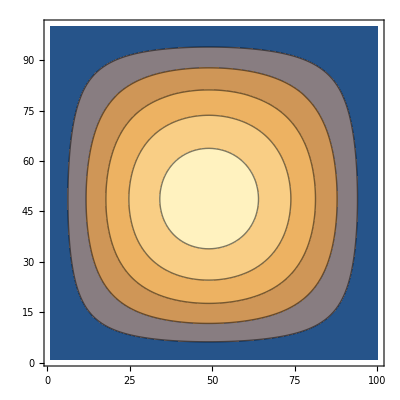

```mathematica
ListContourPlot[V,PlotRange->All]
```